# Infection by SARS-CoV-2 with alternate frequencies of mRNA vaccine boosting for patients undergoing antineoplastic treatment for cancer

Jeffrey P. Townsend, Hayley B. Hassler, Brinda Emu, Alex Dornburg

## SARS-CoV-2 (Gudbjartsson)

Input Data: Average peak-normalized ELIZA ODs for SARS-CoV-2 S1 IgG antibodies from Gudbjartsson et al. 2020, “Humoral Immune Response to SARS-CoV-2 in Iceland”, New England Journal of Medicine. scaled to post-BNT162b2 (Pfizer-BioNTech) booster vaccination level using the average peak value from 110 naive individuals from Kontopoulou et al. 2022 “Significant Increase in Antibody Titers after the 3rd Booster Dose of the Pfizer–BioNTech mRNA COVID-19 Vaccine in Healthcare Workers in Greece”, Vaccines.

days : 34, 48, 70, 94, 109
OD : 1.6, 1.55, 1.43, 1.19, 1.22

```mathematica
sarscov2data={
{1,34, SARSCoV2,1.6/1.6,  TRUE,NA, NA},
{2,48, SARSCoV2,1.55/1.6, FALSE, (48-34), (1.55/1.6-1.6/1.6)/(48-34)},
{3, 70, SARSCoV2,1.43/1.6,  FALSE,(70-48), (1.43/1.6-1.55/1.6)/(70-48)},
{4, 94, SARSCoV2,1.19/1.6, FALSE,(94-70),  (1.19/1.6-1.43/1.6)/(94-70)}
}
```

{{1,34,SARSCoV2,1.,TRUE,NA,NA},{2,48,SARSCoV2,0.96875,FALSE,14,-0.00223214},{3,70,SARSCoV2,0.89375,FALSE,22,-0.00340909},{4,94,SARSCoV2,0.74375,FALSE,24,-0.00625}}

### SARS-CoV-2 Waning of Antibody OD

```mathematica
sarscov2datalength=Length[sarscov2data]
```

4

```mathematica
Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod,  0.75,1, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
sarscov2paddedmeanwaning=Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod, 0.75,1.25, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}},{1.05,{}},{1.1,{}},{1.15,{}},{1.2,{}},{1.25,{}}}

Mean waning extended to chemotherapy BNT162b2-scaled peak (1.219225411) from Peeters et al. 2021.

```mathematica
sarscov2meanwaningTLM={{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.0034090909090909124}},{0.95,{-0.0034090909090909124}},{1.,{-0.002232142857142857}}}
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
TableForm[sarscov2meanwaningTLM]
```

0.75 | -0.00625
0.8 | -0.00625
0.85 | -0.00625
0.9 | -0.00340909
0.95 | -0.00340909
1. | -0.00223214

```mathematica
sarscov2antibodywaningTLM=Interpolation[sarscov2meanwaningTLM]
```

InterpolatingFunction[…]

```mathematica
sarscov2antibodytimecourseTLM={1};
day=1;
While[sarscov2antibodytimecourseTLM[[day]]≥0.75,
sarscov2antibodytimecourseTLM=Append[sarscov2antibodytimecourseTLM, sarscov2antibodytimecourseTLM[[day]]+sarscov2antibodywaningTLM[sarscov2antibodytimecourseTLM[[day]]]];
sarscov2antibodytimecourseTLM=Flatten[sarscov2antibodytimecourseTLM];
Increment[day];
];
sarscov2antibodytimecourseTLM
```

{1,0.997768,0.995402,0.992906,0.990284,0.987541,0.984687,0.981728,0.978675,0.97554,0.972332,0.969064,0.965746,0.962391,0.959008,0.955607,0.952197,0.948786,0.945379,0.941982,0.938598,0.935231,0.931879,0.928545,0.925226,0.921921,0.918624,0.915332,0.912039,0.908738,0.90542,0.902076,0.898696,0.895224,0.891577,0.887733,0.883672,0.879371,0.87481,0.869969,0.864831,0.859383,0.853621,0.84755,0.841257,0.834882,0.828462,0.82203,0.815612,0.809229,0.802894,0.796617,0.790399,0.784236,0.778121,0.772038,0.76597,0.759893,0.753779,0.747592}

```mathematica
sarscov2baseline=0.1641335
```

0.164134

This baseline peak-normalized S IgG antibody level for SARS-CoV-2 comes from the ancestral and descendent states analysis that used the baselines for the human “seasonal” coronaviruses to estimate the baselines for the zoonotic coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
scalarsabove1=Table[(1.422592491177772-0.422592491177772*(index-1)/(Length[sarscov2antibodytimecourseTLM]-1))/1.422592491177772, {index, Length[sarscov2antibodytimecourseTLM]}]
```

{1.,0.994965,0.98993,0.984895,0.97986,0.974826,0.969791,0.964756,0.959721,0.954686,0.949651,0.944616,0.939581,0.934547,0.929512,0.924477,0.919442,0.914407,0.909372,0.904337,0.899302,0.894267,0.889233,0.884198,0.879163,0.874128,0.869093,0.864058,0.859023,0.853988,0.848954,0.843919,0.838884,0.833849,0.828814,0.823779,0.818744,0.813709,0.808675,0.80364,0.798605,0.79357,0.788535,0.7835,0.778465,0.77343,0.768395,0.763361,0.758326,0.753291,0.748256,0.743221,0.738186,0.733151,0.728116,0.723082,0.718047,0.713012,0.707977,0.702942}

```mathematica
sarscov2antibodytimecourseBPtoExp=(sarscov2antibodytimecourseTLM+0.219225411)*scalarsabove1
```

{1.21923,1.21087,1.2024,1.19382,1.18515,1.17639,1.16754,1.15863,1.14965,1.14063,1.13156,1.12248,1.11338,1.10428,1.09518,1.08611,1.07706,1.06804,1.05906,1.05012,1.04123,1.03239,1.0236,1.01486,1.00616,0.997508,0.988897,0.980324,0.971783,0.963267,0.954772,0.946288,0.937806,0.929283,0.920649,0.91189,0.902991,0.893938,0.884719,0.87532,0.865732,0.855951,0.845977,0.835818,0.825548,0.815279,0.805039,0.794854,0.784744,0.774725,0.764807,0.754995,0.745291,0.735689,0.726184,0.716765,0.707416,0.698123,0.688864,0.679617}

```mathematica
Export["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv", sarscov2antibodytimecourseTLM]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

OpenWrite::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv.

$Failed

Used natural infection lambda value imputed in Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2halflife=Log[2]/ lambda /.lambda->0.0044587480795691795
```

155.458

```mathematica
Length[sarscov2antibodytimecourseBPtoExp]
```

60

```mathematica
sarscov2antibodytimecourseB=sarscov2antibodytimecourseBPtoExp;
day=Length[sarscov2antibodytimecourseB];
While[day<4393,
Increment[day];
AppendTo[sarscov2antibodytimecourseB, sarscov2baseline+(sarscov2antibodytimecourseB[[day-1]]- sarscov2baseline)*Exp[-lambda /.lambda->0.0044587480795691795]]
]
```

```mathematica
sarscov2antibodytimecourseB
```

{1.21923,1.21087,1.2024,1.19382,1.18515,1.17639,1.16754,1.15863,1.14965,1.14063,1.13156,1.12248,1.11338,1.10428,1.09518,1.08611,1.07706,1.06804,1.05906,1.05012,1.04123,1.03239,1.0236,1.01486,1.00616,0.997508,0.988897,0.980324,0.971783,0.963267,0.954772,0.946288,0.937806,0.929283,0.920649,0.91189,0.902991,0.893938,0.884719,0.87532,0.865732,0.855951,0.845977,0.835818,0.825548,0.815279,0.805039,0.794854,0.784744,0.774725,0.764807,0.754995,0.745291,0.735689,0.726184,0.716765,0.707416,0.698123,0.688864,0.679617,0.677324,0.67504,0.672768,0.670505,0.668252,0.666009,0.663776,0.661554,0.659341,0.657138,0.654944,0.652761,0.650587,0.648423,0.646268,0.644123,0.641988,0.639862,0.637746,0.635639,0.633541,0.631453,0.629374,0.627304,0.625243,0.623192,0.62115,0.619116,0.617092,0.615077,0.613071,0.611074,0.609085,0.607106,0.605135,0.603173,0.60122,0.599276,0.59734,0.595412,0.593494,0.591584,0.589682,0.587789,0.585904,0.584028,0.58216,0.5803,0.578448,0.576605,0.57477,0.572943,0.571125,0.569314,0.567511,0.565717,0.56393,0.562152,0.560381,0.558618,0.556863,0.555116,0.553377,0.551645,0.549921,0.548205,0.546496,0.544795,0.543101,0.541415,0.539737,0.538066,0.536402,0.534746,0.533097,0.531456,0.529822,0.528195,0.526575,0.524963,0.523358,0.521759,0.520168,0.518585,0.517008,0.515438,0.513875,0.512319,0.51077,0.509228,0.507693,0.506164,0.504642,0.503128,0.501619,0.500118,0.498623,0.497135,0.495654,0.494179,0.492711,0.491249,0.489794,0.488345,0.486902,0.485466,0.484037,0.482614,0.481197,0.479786,0.478382,0.476984,0.475592,0.474206,0.472827,0.471454,0.470086,0.468725,0.46737,0.466021,0.464678,0.463341,0.46201,0.460685,0.459366,0.458052,0.456744,0.455443,0.454147,0.452856,0.451572,0.450293,0.44902,0.447753,0.446491,0.445235,0.443984,0.442739,0.4415,0.440266,0.439037,0.437814,0.436597,0.435385,0.434178,0.432977,0.431781,0.43059,0.429404,0.428224,0.427049,0.42588,0.424715,0.423556,0.422402,0.421253,0.420109,0.41897,0.417836,0.416708,0.415584,0.414465,0.413352,0.412243,0.411139,0.41004,0.408946,0.407857,0.406773,0.405693,0.404619,0.403549,0.402484,0.401423,0.400368,0.399317,0.398271,0.397229,0.396192,0.39516,0.394132,0.393109,0.39209,0.391076,0.390066,0.389061,0.38806,0.387064,0.386072,0.385085,0.384102,0.383123,0.382149,0.381179,0.380214,0.379252,0.378295,0.377342,0.376394,0.37545,0.37451,0.373574,0.372642,0.371714,0.370791,0.369871,0.368956,0.368045,0.367138,0.366235,0.365335,0.36444,0.363549,0.362662,0.361779,0.3609,0.360024,0.359153,0.358285,0.357421,0.356561,0.355705,0.354853,0.354005,0.35316,0.352319,0.351482,0.350648,0.349819,0.348992,0.34817,0.347351,0.346536,0.345725,0.344917,0.344113,0.343312,0.342515,0.341721,0.340931,0.340145,0.339361,0.338582,0.337806,0.337033,0.336264,0.335498,0.334736,0.333977,0.333221,0.332469,0.33172,0.330975,0.330232,0.329493,0.328758,0.328025,0.327296,0.32657,0.325848,0.325128,0.324412,0.323699,0.322989,0.322282,0.321579,0.320878,0.320181,0.319487,0.318796,0.318108,0.317423,0.316741,0.316062,0.315386,0.314713,0.314043,0.313376,0.312712,0.312051,0.311393,0.310738,0.310086,0.309436,0.30879,0.308146,0.307506,0.306868,0.306233,0.305601,0.304971,0.304345,0.303721,0.3031,0.302482,0.301866,0.301254,0.300644,0.300036,0.299432,0.29883,0.29823,0.297634,0.29704,0.296449,0.29586,0.295274,0.294691,0.29411,0.293532,0.292956,0.292383,0.291812,0.291244,0.290679,0.290116,0.289555,0.288997,0.288442,0.287889,0.287338,0.28679,0.286244,0.285701,0.28516,0.284622,0.284086,0.283552,0.283021,0.282492,0.281965,0.281441,0.280919,0.2804,0.279883,0.279368,0.278855,0.278345,0.277836,0.277331,0.276827,0.276326,0.275827,0.27533,0.274835,0.274342,0.273852,0.273364,0.272878,0.272394,0.271913,0.271433,0.270956,0.270481,0.270007,0.269536,0.269068,0.268601,0.268136,0.267673,0.267213,0.266754,0.266298,0.265843,0.265391,0.26494,0.264492,0.264045,0.263601,0.263158,0.262718,0.262279,0.261842,0.261408,0.260975,0.260544,0.260115,0.259688,0.259263,0.25884,0.258418,0.257999,0.257581,0.257166,0.256752,0.25634,0.25593,0.255521,0.255115,0.25471,0.254307,0.253906,0.253506,0.253109,0.252713,0.252319,0.251927,0.251536,0.251147,0.25076,0.250375,0.249991,0.249609,0.249229,0.24885,0.248473,0.248098,0.247724,0.247353,0.246982,0.246614,0.246247,0.245882,0.245518,0.245156,0.244795,0.244437,0.244079,0.243724,0.24337,0.243017,0.242666,0.242317,0.241969,0.241623,0.241278,0.240935,0.240593,0.240253,0.239914,0.239577,0.239241,0.238907,0.238575,0.238243,0.237914,0.237585,0.237259,0.236933,0.23661,0.236287,0.235966,0.235647,0.235328,0.235012,0.234696,0.234382,0.23407,0.233759,0.233449,0.233141,0.232834,0.232528,0.232224,0.231921,0.231619,0.231319,0.23102,0.230723,0.230426,0.230131,0.229838,0.229545,0.229254,0.228965,0.228676,0.228389,0.228103,0.227819,0.227535,0.227253,0.226973,0.226693,0.226415,0.226138,0.225862,0.225587,0.225314,0.225042,0.224771,0.224501,0.224232,0.223965,0.223699,0.223434,0.22317,0.222907,0.222646,0.222385,0.222126,0.221868,0.221611,0.221356,0.221101,0.220848,0.220595,0.220344,0.220094,0.219845,0.219597,0.219351,0.219105,0.21886,0.218617,0.218375,0.218133,0.217893,0.217654,0.217416,0.217179,0.216943,0.216708,0.216474,0.216241,0.216009,0.215778,0.215549,0.21532,0.215092,0.214865,0.21464,0.214415,0.214191,0.213969,0.213747,0.213526,0.213307,0.213088,0.21287,0.212653,0.212437,0.212222,0.212008,0.211795,0.211583,0.211372,0.211162,0.210953,0.210745,0.210537,0.210331,0.210125,0.209921,0.209717,0.209514,0.209312,0.209111,0.208911,0.208712,0.208514,0.208316,0.20812,0.207924,0.207729,0.207535,0.207342,0.20715,0.206959,0.206768,0.206578,0.20639,0.206202,0.206014,0.205828,0.205643,0.205458,0.205274,0.205091,0.204909,0.204727,0.204547,0.204367,0.204188,0.20401,0.203832,0.203656,0.20348,0.203305,0.203131,0.202957,0.202784,0.202613,0.202441,0.202271,0.202101,0.201932,0.201764,0.201597,0.20143,0.201264,0.201099,0.200935,0.200771,0.200608,0.200446,0.200284,0.200123,0.199963,0.199804,0.199645,0.199487,0.19933,0.199173,0.199017,0.198862,0.198708,0.198554,0.198401,0.198248,0.198096,0.197945,0.197795,0.197645,0.197496,0.197348,0.1972,0.197053,0.196906,0.19676,0.196615,0.196471,0.196327,0.196184,0.196041,0.195899,0.195758,0.195617,0.195477,0.195338,0.195199,0.195061,0.194923,0.194786,0.19465,0.194514,0.194379,0.194244,0.19411,0.193977,0.193844,0.193712,0.19358,0.193449,0.193319,0.193189,0.19306,0.192931,0.192803,0.192676,0.192549,0.192422,0.192296,0.192171,0.192046,0.191922,0.191798,0.191675,0.191553,0.191431,0.191309,0.191189,0.191068,0.190948,0.190829,0.19071,0.190592,0.190474,0.190357,0.19024,0.190124,0.190009,0.189894,0.189779,0.189665,0.189551,0.189438,0.189326,0.189214,0.189102,0.188991,0.18888,0.18877,0.188661,0.188552,0.188443,0.188335,0.188227,0.18812,0.188013,0.187907,0.187801,0.187696,0.187591,0.187487,0.187383,0.187279,0.187176,0.187074,0.186972,0.18687,0.186769,0.186668,0.186568,0.186468,0.186369,0.18627,0.186172,0.186073,0.185976,0.185879,0.185782,0.185686,0.18559,0.185494,0.185399,0.185305,0.185211,0.185117,0.185023,0.18493,0.184838,0.184746,0.184654,0.184563,0.184472,0.184381,0.184291,0.184202,0.184112,0.184024,0.183935,0.183847,0.183759,0.183672,0.183585,0.183498,0.183412,0.183327,0.183241,0.183156,0.183072,0.182987,0.182903,0.18282,0.182737,0.182654,0.182572,0.18249,0.182408,0.182327,0.182246,0.182165,0.182085,0.182005,0.181926,0.181846,0.181768,0.181689,0.181611,0.181533,0.181456,0.181379,0.181302,0.181226,0.18115,0.181074,0.180999,0.180924,0.180849,0.180774,0.1807,0.180627,0.180553,0.18048,0.180408,0.180335,0.180263,0.180191,0.18012,0.180049,0.179978,0.179908,0.179837,0.179767,0.179698,0.179629,0.17956,0.179491,0.179423,0.179355,0.179287,0.17922,0.179153,0.179086,0.179019,0.178953,0.178887,0.178821,0.178756,0.178691,0.178626,0.178562,0.178498,0.178434,0.17837,0.178307,0.178244,0.178181,0.178118,0.178056,0.177994,0.177933,0.177871,0.17781,0.177749,0.177689,0.177628,0.177568,0.177509,0.177449,0.17739,0.177331,0.177272,0.177214,0.177155,0.177098,0.17704,0.176982,0.176925,0.176868,0.176812,0.176755,0.176699,0.176643,0.176588,0.176532,0.176477,0.176422,0.176367,0.176313,0.176259,0.176205,0.176151,0.176098,0.176045,0.175992,0.175939,0.175886,0.175834,0.175782,0.17573,0.175678,0.175627,0.175576,0.175525,0.175474,0.175424,0.175374,0.175324,0.175274,0.175224,0.175175,0.175126,0.175077,0.175028,0.17498,0.174932,0.174884,0.174836,0.174788,0.174741,0.174694,0.174647,0.1746,0.174553,0.174507,0.174461,0.174415,0.174369,0.174323,0.174278,0.174233,0.174188,0.174143,0.174099,0.174055,0.17401,0.173966,0.173923,0.173879,0.173836,0.173793,0.17375,0.173707,0.173664,0.173622,0.17358,0.173538,0.173496,0.173454,0.173413,0.173371,0.17333,0.173289,0.173249,0.173208,0.173168,0.173128,0.173088,0.173048,0.173008,0.172969,0.172929,0.17289,0.172851,0.172812,0.172774,0.172735,0.172697,0.172659,0.172621,0.172583,0.172546,0.172508,0.172471,0.172434,0.172397,0.17236,0.172324,0.172287,0.172251,0.172215,0.172179,0.172143,0.172107,0.172072,0.172037,0.172001,0.171966,0.171932,0.171897,0.171862,0.171828,0.171794,0.17176,0.171726,0.171692,0.171658,0.171625,0.171592,0.171558,0.171525,0.171492,0.17146,0.171427,0.171395,0.171362,0.17133,0.171298,0.171266,0.171235,0.171203,0.171172,0.17114,0.171109,0.171078,0.171047,0.171016,0.170986,0.170955,0.170925,0.170895,0.170865,0.170835,0.170805,0.170775,0.170746,0.170716,0.170687,0.170658,0.170629,0.1706,0.170571,0.170542,0.170514,0.170486,0.170457,0.170429,0.170401,0.170373,0.170346,0.170318,0.17029,0.170263,0.170236,0.170209,0.170182,0.170155,0.170128,0.170101,0.170075,0.170048,0.170022,0.169996,0.16997,0.169944,0.169918,0.169892,0.169866,0.169841,0.169816,0.16979,0.169765,0.16974,0.169715,0.16969,0.169666,0.169641,0.169616,0.169592,0.169568,0.169544,0.16952,0.169496,0.169472,0.169448,0.169424,0.169401,0.169377,0.169354,0.169331,0.169308,0.169285,0.169262,0.169239,0.169216,0.169194,0.169171,0.169149,0.169126,0.169104,0.169082,0.16906,0.169038,0.169016,0.168995,0.168973,0.168951,0.16893,0.168909,0.168887,0.168866,0.168845,0.168824,0.168803,0.168783,0.168762,0.168741,0.168721,0.1687,0.16868,0.16866,0.16864,0.16862,0.1686,0.16858,0.16856,0.16854,0.168521,0.168501,0.168482,0.168462,0.168443,0.168424,0.168405,0.168386,0.168367,0.168348,0.168329,0.168311,0.168292,0.168274,0.168255,0.168237,0.168219,0.1682,0.168182,0.168164,0.168146,0.168129,0.168111,0.168093,0.168076,0.168058,0.168041,0.168023,0.168006,0.167989,0.167971,0.167954,0.167937,0.16792,0.167904,0.167887,0.16787,0.167854,0.167837,0.16782,0.167804,0.167788,0.167772,0.167755,0.167739,0.167723,0.167707,0.167691,0.167675,0.16766,0.167644,0.167628,0.167613,0.167597,0.167582,0.167567,0.167551,0.167536,0.167521,0.167506,0.167491,0.167476,0.167461,0.167446,0.167432,0.167417,0.167402,0.167388,0.167373,0.167359,0.167345,0.16733,0.167316,0.167302,0.167288,0.167274,0.16726,0.167246,0.167232,0.167218,0.167205,0.167191,0.167177,0.167164,0.16715,0.167137,0.167123,0.16711,0.167097,0.167084,0.167071,0.167058,0.167045,0.167032,0.167019,0.167006,0.166993,0.16698,0.166968,0.166955,0.166942,0.16693,0.166918,0.166905,0.166893,0.166881,0.166868,0.166856,0.166844,0.166832,0.16682,0.166808,0.166796,0.166784,0.166773,0.166761,0.166749,0.166737,0.166726,0.166714,0.166703,0.166691,0.16668,0.166669,0.166657,0.166646,0.166635,0.166624,0.166613,0.166602,0.166591,0.16658,0.166569,0.166558,0.166547,0.166537,0.166526,0.166515,0.166505,0.166494,0.166484,0.166473,0.166463,0.166452,0.166442,0.166432,0.166422,0.166411,0.166401,0.166391,0.166381,0.166371,0.166361,0.166351,0.166341,0.166332,0.166322,0.166312,0.166302,0.166293,0.166283,0.166274,0.166264,0.166255,0.166245,0.166236,0.166226,0.166217,0.166208,0.166199,0.166189,0.16618,0.166171,0.166162,0.166153,0.166144,0.166135,0.166126,0.166117,0.166109,0.1661,0.166091,0.166082,0.166074,0.166065,0.166056,0.166048,0.166039,0.166031,0.166022,0.166014,0.166006,0.165997,0.165989,0.165981,0.165973,0.165964,0.165956,0.165948,0.16594,0.165932,0.165924,0.165916,0.165908,0.1659,0.165892,0.165885,0.165877,0.165869,0.165861,0.165854,0.165846,0.165838,0.165831,0.165823,0.165816,0.165808,0.165801,0.165793,0.165786,0.165779,0.165771,0.165764,0.165757,0.165749,0.165742,0.165735,0.165728,0.165721,0.165714,0.165707,0.1657,0.165693,0.165686,0.165679,0.165672,0.165665,0.165658,0.165652,0.165645,0.165638,0.165632,0.165625,0.165618,0.165612,0.165605,0.165598,0.165592,0.165585,0.165579,0.165573,0.165566,0.16556,0.165553,0.165547,0.165541,0.165535,0.165528,0.165522,0.165516,0.16551,0.165504,0.165498,0.165492,0.165486,0.165479,0.165474,0.165468,0.165462,0.165456,0.16545,0.165444,0.165438,0.165432,0.165427,0.165421,0.165415,0.165409,0.165404,0.165398,0.165392,0.165387,0.165381,0.165376,0.16537,0.165365,0.165359,0.165354,0.165348,0.165343,0.165338,0.165332,0.165327,0.165322,0.165316,0.165311,0.165306,0.165301,0.165295,0.16529,0.165285,0.16528,0.165275,0.16527,0.165265,0.16526,0.165255,0.16525,0.165245,0.16524,0.165235,0.16523,0.165225,0.16522,0.165215,0.165211,0.165206,0.165201,0.165196,0.165191,0.165187,0.165182,0.165177,0.165173,0.165168,0.165164,0.165159,0.165154,0.16515,0.165145,0.165141,0.165136,0.165132,0.165127,0.165123,0.165119,0.165114,0.16511,0.165106,0.165101,0.165097,0.165093,0.165088,0.165084,0.16508,0.165076,0.165071,0.165067,0.165063,0.165059,0.165055,0.165051,0.165047,0.165043,0.165039,0.165035,0.165031,0.165027,0.165023,0.165019,0.165015,0.165011,0.165007,0.165003,0.164999,0.164995,0.164991,0.164988,0.164984,0.16498,0.164976,0.164973,0.164969,0.164965,0.164961,0.164958,0.164954,0.16495,0.164947,0.164943,0.16494,0.164936,0.164932,0.164929,0.164925,0.164922,0.164918,0.164915,0.164911,0.164908,0.164904,0.164901,0.164898,0.164894,0.164891,0.164887,0.164884,0.164881,0.164877,0.164874,0.164871,0.164867,0.164864,0.164861,0.164858,0.164855,0.164851,0.164848,0.164845,0.164842,0.164839,0.164835,0.164832,0.164829,0.164826,0.164823,0.16482,0.164817,0.164814,0.164811,0.164808,0.164805,0.164802,0.164799,0.164796,0.164793,0.16479,0.164787,0.164784,0.164781,0.164778,0.164776,0.164773,0.16477,0.164767,0.164764,0.164761,0.164759,0.164756,0.164753,0.16475,0.164748,0.164745,0.164742,0.164739,0.164737,0.164734,0.164731,0.164729,0.164726,0.164723,0.164721,0.164718,0.164716,0.164713,0.16471,0.164708,0.164705,0.164703,0.1647,0.164698,0.164695,0.164693,0.16469,0.164688,0.164685,0.164683,0.16468,0.164678,0.164676,0.164673,0.164671,0.164668,0.164666,0.164664,0.164661,0.164659,0.164657,0.164654,0.164652,0.16465,0.164647,0.164645,0.164643,0.16464,0.164638,0.164636,0.164634,0.164631,0.164629,0.164627,0.164625,0.164623,0.164621,0.164618,0.164616,0.164614,0.164612,0.16461,0.164608,0.164606,0.164603,0.164601,0.164599,0.164597,0.164595,0.164593,0.164591,0.164589,0.164587,0.164585,0.164583,0.164581,0.164579,0.164577,0.164575,0.164573,0.164571,0.164569,0.164567,0.164565,0.164563,0.164561,0.16456,0.164558,0.164556,0.164554,0.164552,0.16455,0.164548,0.164546,0.164545,0.164543,0.164541,0.164539,0.164537,0.164536,0.164534,0.164532,0.16453,0.164528,0.164527,0.164525,0.164523,0.164521,0.16452,0.164518,0.164516,0.164515,0.164513,0.164511,0.16451,0.164508,0.164506,0.164505,0.164503,0.164501,0.1645,0.164498,0.164496,0.164495,0.164493,0.164492,0.16449,0.164488,0.164487,0.164485,0.164484,0.164482,0.164481,0.164479,0.164477,0.164476,0.164474,0.164473,0.164471,0.16447,0.164468,0.164467,0.164465,0.164464,0.164462,0.164461,0.16446,0.164458,0.164457,0.164455,0.164454,0.164452,0.164451,0.16445,0.164448,0.164447,0.164445,0.164444,0.164443,0.164441,0.16444,0.164438,0.164437,0.164436,0.164434,0.164433,0.164432,0.16443,0.164429,0.164428,0.164426,0.164425,0.164424,0.164423,0.164421,0.16442,0.164419,0.164417,0.164416,0.164415,0.164414,0.164412,0.164411,0.16441,0.164409,0.164407,0.164406,0.164405,0.164404,0.164403,0.164401,0.1644,0.164399,0.164398,0.164397,0.164396,0.164394,0.164393,0.164392,0.164391,0.16439,0.164389,0.164387,0.164386,0.164385,0.164384,0.164383,0.164382,0.164381,0.16438,0.164379,0.164378,0.164376,0.164375,0.164374,0.164373,0.164372,0.164371,0.16437,0.164369,0.164368,0.164367,0.164366,0.164365,0.164364,0.164363,0.164362,0.164361,0.16436,0.164359,0.164358,0.164357,0.164356,0.164355,0.164354,0.164353,0.164352,0.164351,0.16435,0.164349,0.164348,0.164347,0.164346,0.164345,0.164344,0.164343,0.164342,0.164341,0.16434,0.164339,0.164339,0.164338,0.164337,0.164336,0.164335,0.164334,0.164333,0.164332,0.164331,0.16433,0.16433,0.164329,0.164328,0.164327,0.164326,0.164325,0.164324,0.164324,0.164323,0.164322,0.164321,0.16432,0.164319,0.164319,0.164318,0.164317,0.164316,0.164315,0.164314,0.164314,0.164313,0.164312,0.164311,0.164311,0.16431,0.164309,0.164308,0.164307,0.164307,0.164306,0.164305,0.164304,0.164304,0.164303,0.164302,0.164301,0.164301,0.1643,0.164299,0.164298,0.164298,0.164297,0.164296,0.164295,0.164295,0.164294,0.164293,0.164293,0.164292,0.164291,0.16429,0.16429,0.164289,0.164288,0.164288,0.164287,0.164286,0.164286,0.164285,0.164284,0.164284,0.164283,0.164282,0.164282,0.164281,0.16428,0.16428,0.164279,0.164278,0.164278,0.164277,0.164276,0.164276,0.164275,0.164275,0.164274,0.164273,0.164273,0.164272,0.164271,0.164271,0.16427,0.16427,0.164269,0.164268,0.164268,0.164267,0.164267,0.164266,0.164265,0.164265,0.164264,0.164264,0.164263,0.164262,0.164262,0.164261,0.164261,0.16426,0.16426,0.164259,0.164259,0.164258,0.164257,0.164257,0.164256,0.164256,0.164255,0.164255,0.164254,0.164254,0.164253,0.164253,0.164252,0.164251,0.164251,0.16425,0.16425,0.164249,0.164249,0.164248,0.164248,0.164247,0.164247,0.164246,0.164246,0.164245,0.164245,0.164244,0.164244,0.164243,0.164243,0.164242,0.164242,0.164241,0.164241,0.16424,0.16424,0.164239,0.164239,0.164239,0.164238,0.164238,0.164237,0.164237,0.164236,0.164236,0.164235,0.164235,0.164234,0.164234,0.164234,0.164233,0.164233,0.164232,0.164232,0.164231,0.164231,0.16423,0.16423,0.16423,0.164229,0.164229,0.164228,0.164228,0.164227,0.164227,0.164227,0.164226,0.164226,0.164225,0.164225,0.164225,0.164224,0.164224,0.164223,0.164223,0.164223,0.164222,0.164222,0.164221,0.164221,0.164221,0.16422,0.16422,0.164219,0.164219,0.164219,0.164218,0.164218,0.164218,0.164217,0.164217,0.164216,0.164216,0.164216,0.164215,0.164215,0.164215,0.164214,0.164214,0.164214,0.164213,0.164213,0.164212,0.164212,0.164212,0.164211,0.164211,0.164211,0.16421,0.16421,0.16421,0.164209,0.164209,0.164209,0.164208,0.164208,0.164208,0.164207,0.164207,0.164207,0.164206,0.164206,0.164206,0.164205,0.164205,0.164205,0.164204,0.164204,0.164204,0.164204,0.164203,0.164203,0.164203,0.164202,0.164202,0.164202,0.164201,0.164201,0.164201,0.1642,0.1642,0.1642,0.1642,0.164199,0.164199,0.164199,0.164198,0.164198,0.164198,0.164198,0.164197,0.164197,0.164197,0.164196,0.164196,0.164196,0.164196,0.164195,0.164195,0.164195,0.164194,0.164194,0.164194,0.164194,0.164193,0.164193,0.164193,0.164193,0.164192,0.164192,0.164192,0.164192,0.164191,0.164191,0.164191,0.164191,0.16419,0.16419,0.16419,0.16419,0.164189,0.164189,0.164189,0.164189,0.164188,0.164188,0.164188,0.164188,0.164187,0.164187,0.164187,0.164187,0.164186,0.164186,0.164186,0.164186,0.164185,0.164185,0.164185,0.164185,0.164185,0.164184,0.164184,0.164184,0.164184,0.164183,0.164183,0.164183,0.164183,0.164183,0.164182,0.164182,0.164182,0.164182,0.164181,0.164181,0.164181,0.164181,0.164181,0.16418,0.16418,0.16418,0.16418,0.16418,0.164179,0.164179,0.164179,0.164179,0.164179,0.164178,0.164178,0.164178,0.164178,0.164178,0.164177,0.164177,0.164177,0.164177,0.164177,0.164176,0.164176,0.164176,0.164176,0.164176,0.164175,0.164175,0.164175,0.164175,0.164175,0.164175,0.164174,0.164174,0.164174,0.164174,0.164174,0.164173,0.164173,0.164173,0.164173,0.164173,0.164173,0.164172,0.164172,0.164172,0.164172,0.164172,0.164172,0.164171,0.164171,0.164171,0.164171,0.164171,0.164171,0.16417,0.16417,0.16417,0.16417,0.16417,0.16417,0.164169,0.164169,0.164169,0.164169,0.164169,0.164169,0.164168,0.164168,0.164168,0.164168,0.164168,0.164168,0.164168,0.164167,0.164167,0.164167,0.164167,0.164167,0.164167,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134}

```mathematica
sarscov2antibodytimecourseB[[150]]
```

0.509228

```mathematica
1.675000077*(10^3.02)/(10^3.373)
```

0.743045

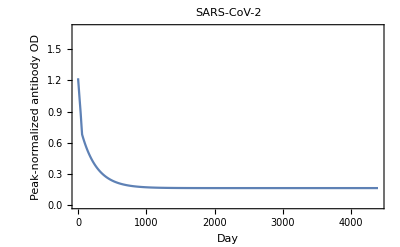

```mathematica
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster04May2023.pdf.

$Failed

### SARS-CoV-2 Probability of Infection | Antibody OD

```mathematica
sarscov2probinfgivenaod[aod_]:=1/(1+Exp[-(-5.841733+-5.323444*aod)])
```

These values for a and b come from the ancestral and descendent states natural infection analysis to determine them for the zoonotic coronaviruses given baselines and declines for all viruses, and a’s and b’s for the “seasonal” coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2probinfgivenaod[aod]
```

1/(1+ⅇ^(5.84173+5.32344 aod))

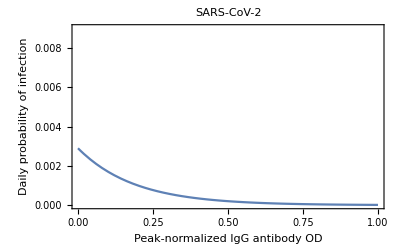

```mathematica
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster04May2023.pdf.

$Failed

```mathematica
sarscov2probinfgivenall[a_, b_, aod_]:=1/(1+Exp[-(a+b*aod)])
```

### SARS-CoV-2 Probability of No Reinfection Time Course

```mathematica
sarscov2probnoreinfectiontimecourse={1};
day=1;
AppendTo[sarscov2probnoreinfectiontimecourse, 
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]]])
];

While[day<4393,
Increment[day];
AppendTo[sarscov2probnoreinfectiontimecourse, 
If[day<Length[sarscov2antibodytimecourseB],
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]] ]),
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]])
]
]
];

sarscov2probnoreinfectiontimecourse
```

{1,0.999995,0.999991,0.999986,0.99998,0.999975,0.999969,0.999963,0.999956,0.99995,0.999943,0.999935,0.999928,0.999919,0.999911,0.999902,0.999893,0.999883,0.999872,0.999862,0.99985,0.999838,0.999826,0.999813,0.999799,0.999785,0.99977,0.999754,0.999737,0.99972,0.999702,0.999683,0.999664,0.999643,0.999621,0.999599,0.999575,0.99955,0.999524,0.999497,0.999468,0.999437,0.999405,0.999371,0.999335,0.999298,0.999258,0.999215,0.999171,0.999124,0.999075,0.999022,0.998968,0.99891,0.998849,0.998785,0.998718,0.998648,0.998573,0.998496,0.998417,0.998337,0.998256,0.998175,0.998092,0.998009,0.997924,0.997838,0.997752,0.997664,0.997575,0.997486,0.997395,0.997303,0.99721,0.997116,0.997022,0.996926,0.996828,0.99673,0.996631,0.996531,0.996429,0.996327,0.996223,0.996118,0.996012,0.995905,0.995797,0.995687,0.995577,0.995465,0.995352,0.995238,0.995123,0.995006,0.994889,0.99477,0.994649,0.994528,0.994406,0.994282,0.994157,0.99403,0.993903,0.993774,0.993644,0.993513,0.99338,0.993246,0.993111,0.992974,0.992836,0.992697,0.992557,0.992415,0.992272,0.992127,0.991981,0.991834,0.991685,0.991536,0.991384,0.991232,0.991077,0.990922,0.990765,0.990607,0.990447,0.990286,0.990124,0.98996,0.989794,0.989628,0.989459,0.98929,0.989119,0.988946,0.988772,0.988597,0.98842,0.988241,0.988061,0.98788,0.987697,0.987512,0.987326,0.987139,0.98695,0.98676,0.986567,0.986374,0.986179,0.985982,0.985784,0.985584,0.985383,0.98518,0.984976,0.98477,0.984562,0.984353,0.984143,0.98393,0.983716,0.983501,0.983284,0.983065,0.982845,0.982623,0.9824,0.982174,0.981948,0.981719,0.981489,0.981258,0.981025,0.98079,0.980553,0.980315,0.980075,0.979834,0.97959,0.979346,0.979099,0.978851,0.978601,0.97835,0.978097,0.977842,0.977585,0.977327,0.977067,0.976806,0.976542,0.976277,0.976011,0.975742,0.975472,0.9752,0.974927,0.974652,0.974375,0.974096,0.973816,0.973534,0.97325,0.972965,0.972678,0.972389,0.972098,0.971806,0.971512,0.971216,0.970918,0.970619,0.970318,0.970015,0.969711,0.969404,0.969096,0.968787,0.968475,0.968162,0.967847,0.96753,0.967212,0.966892,0.96657,0.966246,0.965921,0.965593,0.965264,0.964934,0.964601,0.964267,0.963931,0.963594,0.963254,0.962913,0.96257,0.962225,0.961879,0.961531,0.961181,0.960829,0.960476,0.960121,0.959764,0.959405,0.959045,0.958683,0.958319,0.957953,0.957586,0.957217,0.956846,0.956473,0.956099,0.955723,0.955345,0.954965,0.954584,0.954201,0.953816,0.95343,0.953042,0.952652,0.95226,0.951867,0.951471,0.951075,0.950676,0.950276,0.949874,0.94947,0.949065,0.948657,0.948249,0.947838,0.947426,0.947012,0.946596,0.946179,0.94576,0.945339,0.944917,0.944493,0.944067,0.943639,0.94321,0.942779,0.942347,0.941913,0.941477,0.941039,0.9406,0.940159,0.939717,0.939272,0.938827,0.938379,0.93793,0.937479,0.937027,0.936573,0.936117,0.93566,0.935201,0.93474,0.934278,0.933814,0.933349,0.932882,0.932413,0.931943,0.931471,0.930998,0.930523,0.930046,0.929568,0.929089,0.928607,0.928124,0.92764,0.927154,0.926666,0.926177,0.925687,0.925194,0.924701,0.924205,0.923708,0.92321,0.92271,0.922209,0.921706,0.921201,0.920695,0.920188,0.919679,0.919169,0.918657,0.918143,0.917628,0.917112,0.916594,0.916075,0.915554,0.915032,0.914508,0.913983,0.913456,0.912928,0.912399,0.911868,0.911336,0.910802,0.910267,0.90973,0.909192,0.908653,0.908112,0.90757,0.907026,0.906482,0.905935,0.905388,0.904839,0.904288,0.903737,0.903183,0.902629,0.902073,0.901516,0.900958,0.900398,0.899837,0.899275,0.898711,0.898146,0.89758,0.897012,0.896444,0.895874,0.895302,0.89473,0.894156,0.893581,0.893004,0.892427,0.891848,0.891268,0.890686,0.890104,0.88952,0.888935,0.888349,0.887761,0.887173,0.886583,0.885992,0.8854,0.884807,0.884212,0.883617,0.88302,0.882422,0.881823,0.881223,0.880621,0.880019,0.879415,0.878811,0.878205,0.877598,0.87699,0.876381,0.875771,0.875159,0.874547,0.873934,0.873319,0.872704,0.872087,0.87147,0.870851,0.870231,0.869611,0.868989,0.868366,0.867743,0.867118,0.866492,0.865866,0.865238,0.864609,0.86398,0.863349,0.862717,0.862085,0.861451,0.860817,0.860182,0.859545,0.858908,0.85827,0.857631,0.856991,0.85635,0.855709,0.855066,0.854422,0.853778,0.853133,0.852487,0.85184,0.851192,0.850543,0.849894,0.849243,0.848592,0.84794,0.847287,0.846634,0.845979,0.845324,0.844668,0.844011,0.843354,0.842695,0.842036,0.841376,0.840715,0.840054,0.839392,0.838729,0.838065,0.837401,0.836736,0.83607,0.835403,0.834736,0.834068,0.833399,0.83273,0.83206,0.831389,0.830718,0.830046,0.829373,0.8287,0.828026,0.827351,0.826676,0.826,0.825323,0.824646,0.823968,0.82329,0.822611,0.821931,0.821251,0.82057,0.819889,0.819207,0.818524,0.817841,0.817158,0.816474,0.815789,0.815103,0.814418,0.813731,0.813044,0.812357,0.811669,0.810981,0.810292,0.809602,0.808912,0.808222,0.807531,0.806839,0.806148,0.805455,0.804762,0.804069,0.803375,0.802681,0.801987,0.801292,0.800596,0.7999,0.799204,0.798507,0.79781,0.797112,0.796414,0.795716,0.795017,0.794318,0.793619,0.792919,0.792219,0.791518,0.790817,0.790116,0.789414,0.788712,0.78801,0.787307,0.786604,0.785901,0.785197,0.784493,0.783789,0.783084,0.782379,0.781674,0.780969,0.780263,0.779557,0.778851,0.778144,0.777437,0.77673,0.776023,0.775315,0.774607,0.773899,0.773191,0.772482,0.771774,0.771065,0.770355,0.769646,0.768936,0.768226,0.767516,0.766806,0.766096,0.765385,0.764674,0.763963,0.763252,0.762541,0.761829,0.761117,0.760406,0.759694,0.758981,0.758269,0.757557,0.756844,0.756132,0.755419,0.754706,0.753993,0.75328,0.752566,0.751853,0.75114,0.750426,0.749713,0.748999,0.748285,0.747571,0.746857,0.746143,0.745429,0.744715,0.744001,0.743286,0.742572,0.741858,0.741143,0.740429,0.739714,0.739,0.738285,0.737571,0.736856,0.736141,0.735427,0.734712,0.733998,0.733283,0.732568,0.731854,0.731139,0.730425,0.72971,0.728995,0.728281,0.727566,0.726852,0.726137,0.725423,0.724709,0.723994,0.72328,0.722566,0.721852,0.721138,0.720424,0.71971,0.718996,0.718282,0.717569,0.716855,0.716141,0.715428,0.714715,0.714001,0.713288,0.712575,0.711862,0.711149,0.710437,0.709724,0.709011,0.708299,0.707587,0.706875,0.706163,0.705451,0.704739,0.704028,0.703316,0.702605,0.701894,0.701183,0.700472,0.699761,0.699051,0.69834,0.69763,0.69692,0.696211,0.695501,0.694791,0.694082,0.693373,0.692664,0.691955,0.691247,0.690539,0.689831,0.689123,0.688415,0.687707,0.687,0.686293,0.685586,0.68488,0.684173,0.683467,0.682761,0.682055,0.68135,0.680645,0.67994,0.679235,0.67853,0.677826,0.677122,0.676418,0.675715,0.675011,0.674308,0.673606,0.672903,0.672201,0.671499,0.670797,0.670096,0.669395,0.668694,0.667994,0.667293,0.666593,0.665894,0.665194,0.664495,0.663796,0.663098,0.6624,0.661702,0.661004,0.660307,0.65961,0.658913,0.658217,0.657521,0.656825,0.656129,0.655434,0.65474,0.654045,0.653351,0.652657,0.651964,0.651271,0.650578,0.649885,0.649193,0.648501,0.64781,0.647119,0.646428,0.645738,0.645048,0.644358,0.643669,0.64298,0.642291,0.641603,0.640915,0.640228,0.639541,0.638854,0.638168,0.637482,0.636796,0.636111,0.635426,0.634741,0.634057,0.633373,0.63269,0.632007,0.631325,0.630642,0.629961,0.629279,0.628598,0.627918,0.627237,0.626558,0.625878,0.625199,0.624521,0.623842,0.623165,0.622487,0.62181,0.621134,0.620458,0.619782,0.619107,0.618432,0.617757,0.617083,0.61641,0.615737,0.615064,0.614392,0.61372,0.613048,0.612377,0.611707,0.611036,0.610367,0.609697,0.609029,0.60836,0.607692,0.607025,0.606358,0.605691,0.605025,0.604359,0.603694,0.603029,0.602365,0.601701,0.601037,0.600374,0.599712,0.59905,0.598388,0.597727,0.597066,0.596406,0.595746,0.595087,0.594428,0.59377,0.593112,0.592454,0.591797,0.591141,0.590485,0.589829,0.589174,0.58852,0.587866,0.587212,0.586559,0.585906,0.585254,0.584602,0.583951,0.5833,0.58265,0.582,0.581351,0.580702,0.580054,0.579406,0.578759,0.578112,0.577466,0.57682,0.576174,0.57553,0.574885,0.574241,0.573598,0.572955,0.572313,0.571671,0.57103,0.570389,0.569748,0.569108,0.568469,0.56783,0.567192,0.566554,0.565917,0.56528,0.564644,0.564008,0.563373,0.562738,0.562104,0.56147,0.560837,0.560204,0.559572,0.55894,0.558309,0.557678,0.557048,0.556419,0.55579,0.555161,0.554533,0.553906,0.553279,0.552652,0.552026,0.551401,0.550776,0.550151,0.549528,0.548904,0.548281,0.547659,0.547037,0.546416,0.545796,0.545175,0.544556,0.543937,0.543318,0.5427,0.542083,0.541466,0.540849,0.540233,0.539618,0.539003,0.538389,0.537775,0.537162,0.536549,0.535937,0.535325,0.534714,0.534104,0.533494,0.532884,0.532275,0.531667,0.531059,0.530452,0.529845,0.529239,0.528633,0.528028,0.527423,0.526819,0.526216,0.525613,0.525011,0.524409,0.523807,0.523207,0.522606,0.522007,0.521407,0.520809,0.520211,0.519613,0.519016,0.51842,0.517824,0.517229,0.516634,0.51604,0.515446,0.514853,0.51426,0.513668,0.513077,0.512486,0.511895,0.511306,0.510716,0.510128,0.509539,0.508952,0.508365,0.507778,0.507192,0.506607,0.506022,0.505438,0.504854,0.504271,0.503688,0.503106,0.502524,0.501943,0.501363,0.500783,0.500204,0.499625,0.499047,0.498469,0.497892,0.497315,0.496739,0.496164,0.495589,0.495014,0.494441,0.493867,0.493295,0.492723,0.492151,0.49158,0.491009,0.49044,0.48987,0.489301,0.488733,0.488165,0.487598,0.487032,0.486466,0.4859,0.485335,0.484771,0.484207,0.483644,0.483081,0.482519,0.481957,0.481396,0.480836,0.480276,0.479717,0.479158,0.4786,0.478042,0.477485,0.476928,0.476372,0.475817,0.475262,0.474707,0.474153,0.4736,0.473047,0.472495,0.471944,0.471393,0.470842,0.470292,0.469743,0.469194,0.468646,0.468098,0.467551,0.467004,0.466458,0.465913,0.465368,0.464824,0.46428,0.463736,0.463194,0.462652,0.46211,0.461569,0.461028,0.460488,0.459949,0.45941,0.458872,0.458334,0.457797,0.45726,0.456724,0.456189,0.455654,0.455119,0.454585,0.454052,0.453519,0.452987,0.452455,0.451924,0.451394,0.450864,0.450334,0.449805,0.449277,0.448749,0.448222,0.447695,0.447169,0.446643,0.446118,0.445594,0.44507,0.444546,0.444023,0.443501,0.442979,0.442458,0.441937,0.441417,0.440898,0.440379,0.43986,0.439342,0.438825,0.438308,0.437792,0.437276,0.436761,0.436246,0.435732,0.435218,0.434705,0.434193,0.433681,0.433169,0.432658,0.432148,0.431638,0.431129,0.43062,0.430112,0.429605,0.429098,0.428591,0.428085,0.42758,0.427075,0.42657,0.426067,0.425563,0.425061,0.424558,0.424057,0.423556,0.423055,0.422555,0.422055,0.421556,0.421058,0.42056,0.420063,0.419566,0.41907,0.418574,0.418079,0.417584,0.41709,0.416596,0.416103,0.415611,0.415119,0.414627,0.414136,0.413646,0.413156,0.412667,0.412178,0.411689,0.411202,0.410715,0.410228,0.409742,0.409256,0.408771,0.408286,0.407802,0.407319,0.406836,0.406353,0.405872,0.40539,0.404909,0.404429,0.403949,0.40347,0.402991,0.402513,0.402035,0.401558,0.401081,0.400605,0.40013,0.399654,0.39918,0.398706,0.398232,0.397759,0.397287,0.396815,0.396343,0.395873,0.395402,0.394932,0.394463,0.393994,0.393526,0.393058,0.392591,0.392124,0.391658,0.391192,0.390727,0.390262,0.389798,0.389334,0.388871,0.388408,0.387946,0.387485,0.387024,0.386563,0.386103,0.385644,0.385184,0.384726,0.384268,0.38381,0.383353,0.382897,0.382441,0.381986,0.381531,0.381076,0.380622,0.380169,0.379716,0.379263,0.378812,0.37836,0.377909,0.377459,0.377009,0.37656,0.376111,0.375662,0.375215,0.374767,0.37432,0.373874,0.373428,0.372983,0.372538,0.372094,0.37165,0.371207,0.370764,0.370321,0.369879,0.369438,0.368997,0.368557,0.368117,0.367678,0.367239,0.366801,0.366363,0.365925,0.365488,0.365052,0.364616,0.364181,0.363746,0.363311,0.362878,0.362444,0.362011,0.361579,0.361147,0.360715,0.360284,0.359854,0.359424,0.358994,0.358565,0.358137,0.357709,0.357281,0.356854,0.356428,0.356002,0.355576,0.355151,0.354726,0.354302,0.353879,0.353455,0.353033,0.35261,0.352189,0.351767,0.351347,0.350926,0.350507,0.350087,0.349668,0.34925,0.348832,0.348415,0.347998,0.347581,0.347165,0.34675,0.346335,0.34592,0.345506,0.345093,0.34468,0.344267,0.343855,0.343443,0.343032,0.342621,0.342211,0.341801,0.341392,0.340983,0.340574,0.340166,0.339759,0.339352,0.338945,0.338539,0.338134,0.337729,0.337324,0.33692,0.336516,0.336113,0.33571,0.335308,0.334906,0.334505,0.334104,0.333703,0.333303,0.332904,0.332505,0.332106,0.331708,0.33131,0.330913,0.330516,0.33012,0.329724,0.329328,0.328933,0.328539,0.328145,0.327751,0.327358,0.326966,0.326573,0.326182,0.32579,0.325399,0.325009,0.324619,0.32423,0.323841,0.323452,0.323064,0.322676,0.322289,0.321902,0.321516,0.32113,0.320744,0.320359,0.319975,0.319591,0.319207,0.318824,0.318441,0.318059,0.317677,0.317296,0.316915,0.316534,0.316154,0.315774,0.315395,0.315016,0.314638,0.31426,0.313883,0.313506,0.313129,0.312753,0.312377,0.312002,0.311627,0.311253,0.310879,0.310505,0.310132,0.30976,0.309388,0.309016,0.308645,0.308274,0.307903,0.307533,0.307164,0.306794,0.306426,0.306057,0.30569,0.305322,0.304955,0.304589,0.304222,0.303857,0.303491,0.303127,0.302762,0.302398,0.302035,0.301671,0.301309,0.300946,0.300585,0.300223,0.299862,0.299501,0.299141,0.298782,0.298422,0.298063,0.297705,0.297347,0.296989,0.296632,0.296275,0.295919,0.295563,0.295207,0.294852,0.294497,0.294143,0.293789,0.293436,0.293083,0.29273,0.292378,0.292026,0.291674,0.291323,0.290973,0.290623,0.290273,0.289924,0.289575,0.289226,0.288878,0.28853,0.288183,0.287836,0.28749,0.287144,0.286798,0.286453,0.286108,0.285764,0.28542,0.285076,0.284733,0.28439,0.284048,0.283706,0.283364,0.283023,0.282682,0.282342,0.282002,0.281662,0.281323,0.280984,0.280646,0.280308,0.27997,0.279633,0.279296,0.27896,0.278624,0.278288,0.277953,0.277618,0.277284,0.27695,0.276616,0.276283,0.27595,0.275618,0.275286,0.274954,0.274623,0.274292,0.273962,0.273632,0.273302,0.272973,0.272644,0.272315,0.271987,0.271659,0.271332,0.271005,0.270678,0.270352,0.270026,0.269701,0.269376,0.269051,0.268727,0.268403,0.26808,0.267757,0.267434,0.267112,0.26679,0.266468,0.266147,0.265826,0.265506,0.265186,0.264866,0.264547,0.264228,0.263909,0.263591,0.263273,0.262956,0.262639,0.262322,0.262006,0.26169,0.261374,0.261059,0.260745,0.26043,0.260116,0.259802,0.259489,0.259176,0.258864,0.258552,0.25824,0.257928,0.257617,0.257307,0.256996,0.256686,0.256377,0.256068,0.255759,0.25545,0.255142,0.254834,0.254527,0.25422,0.253913,0.253607,0.253301,0.252996,0.252691,0.252386,0.252081,0.251777,0.251473,0.25117,0.250867,0.250564,0.250262,0.24996,0.249659,0.249357,0.249057,0.248756,0.248456,0.248156,0.247857,0.247558,0.247259,0.246961,0.246663,0.246365,0.246068,0.245771,0.245474,0.245178,0.244882,0.244587,0.244291,0.243997,0.243702,0.243408,0.243114,0.242821,0.242528,0.242235,0.241943,0.241651,0.241359,0.241068,0.240777,0.240486,0.240196,0.239906,0.239617,0.239327,0.239038,0.23875,0.238462,0.238174,0.237886,0.237599,0.237312,0.237026,0.23674,0.236454,0.236169,0.235883,0.235599,0.235314,0.23503,0.234746,0.234463,0.23418,0.233897,0.233615,0.233333,0.233051,0.23277,0.232489,0.232208,0.231928,0.231647,0.231368,0.231088,0.230809,0.230531,0.230252,0.229974,0.229697,0.229419,0.229142,0.228865,0.228589,0.228313,0.228037,0.227762,0.227487,0.227212,0.226938,0.226664,0.22639,0.226117,0.225843,0.225571,0.225298,0.225026,0.224754,0.224483,0.224212,0.223941,0.223671,0.2234,0.223131,0.222861,0.222592,0.222323,0.222054,0.221786,0.221518,0.221251,0.220984,0.220717,0.22045,0.220184,0.219918,0.219652,0.219387,0.219122,0.218857,0.218593,0.218329,0.218065,0.217801,0.217538,0.217275,0.217013,0.216751,0.216489,0.216227,0.215966,0.215705,0.215445,0.215184,0.214924,0.214665,0.214405,0.214146,0.213887,0.213629,0.213371,0.213113,0.212856,0.212598,0.212342,0.212085,0.211829,0.211573,0.211317,0.211062,0.210807,0.210552,0.210298,0.210043,0.20979,0.209536,0.209283,0.20903,0.208777,0.208525,0.208273,0.208021,0.20777,0.207519,0.207268,0.207018,0.206768,0.206518,0.206268,0.206019,0.20577,0.205521,0.205273,0.205025,0.204777,0.204529,0.204282,0.204035,0.203789,0.203542,0.203296,0.203051,0.202805,0.20256,0.202315,0.202071,0.201827,0.201583,0.201339,0.201096,0.200853,0.20061,0.200367,0.200125,0.199883,0.199642,0.1994,0.199159,0.198919,0.198678,0.198438,0.198198,0.197959,0.197719,0.19748,0.197241,0.197003,0.196765,0.196527,0.196289,0.196052,0.195815,0.195578,0.195342,0.195106,0.19487,0.194634,0.194399,0.194164,0.193929,0.193695,0.193461,0.193227,0.192993,0.19276,0.192527,0.192294,0.192062,0.19183,0.191598,0.191366,0.191135,0.190904,0.190673,0.190442,0.190212,0.189982,0.189752,0.189523,0.189294,0.189065,0.188836,0.188608,0.18838,0.188152,0.187925,0.187697,0.18747,0.187244,0.187017,0.186791,0.186565,0.18634,0.186115,0.185889,0.185665,0.18544,0.185216,0.184992,0.184768,0.184545,0.184322,0.184099,0.183876,0.183654,0.183432,0.18321,0.182988,0.182767,0.182546,0.182325,0.182105,0.181885,0.181665,0.181445,0.181226,0.181007,0.180788,0.180569,0.180351,0.180133,0.179915,0.179697,0.17948,0.179263,0.179046,0.178829,0.178613,0.178397,0.178181,0.177966,0.177751,0.177536,0.177321,0.177107,0.176892,0.176679,0.176465,0.176251,0.176038,0.175825,0.175613,0.1754,0.175188,0.174976,0.174765,0.174553,0.174342,0.174131,0.173921,0.17371,0.1735,0.17329,0.173081,0.172872,0.172662,0.172454,0.172245,0.172037,0.171829,0.171621,0.171413,0.171206,0.170999,0.170792,0.170585,0.170379,0.170173,0.169967,0.169762,0.169556,0.169351,0.169146,0.168942,0.168737,0.168533,0.168329,0.168126,0.167922,0.167719,0.167517,0.167314,0.167111,0.166909,0.166707,0.166506,0.166304,0.166103,0.165902,0.165702,0.165501,0.165301,0.165101,0.164901,0.164702,0.164503,0.164304,0.164105,0.163906,0.163708,0.16351,0.163312,0.163115,0.162917,0.16272,0.162523,0.162327,0.162131,0.161934,0.161738,0.161543,0.161347,0.161152,0.160957,0.160763,0.160568,0.160374,0.16018,0.159986,0.159793,0.159599,0.159406,0.159213,0.159021,0.158828,0.158636,0.158444,0.158253,0.158061,0.15787,0.157679,0.157488,0.157298,0.157107,0.156917,0.156727,0.156538,0.156348,0.156159,0.15597,0.155782,0.155593,0.155405,0.155217,0.155029,0.154842,0.154654,0.154467,0.15428,0.154094,0.153907,0.153721,0.153535,0.153349,0.153164,0.152978,0.152793,0.152608,0.152424,0.152239,0.152055,0.151871,0.151688,0.151504,0.151321,0.151138,0.150955,0.150772,0.15059,0.150408,0.150226,0.150044,0.149862,0.149681,0.1495,0.149319,0.149138,0.148958,0.148778,0.148598,0.148418,0.148238,0.148059,0.14788,0.147701,0.147522,0.147344,0.147165,0.146987,0.146809,0.146632,0.146454,0.146277,0.1461,0.145923,0.145747,0.14557,0.145394,0.145218,0.145043,0.144867,0.144692,0.144517,0.144342,0.144167,0.143993,0.143819,0.143645,0.143471,0.143297,0.143124,0.142951,0.142778,0.142605,0.142432,0.14226,0.142088,0.141916,0.141744,0.141573,0.141401,0.14123,0.141059,0.140889,0.140718,0.140548,0.140378,0.140208,0.140038,0.139869,0.1397,0.139531,0.139362,0.139193,0.139025,0.138857,0.138689,0.138521,0.138353,0.138186,0.138018,0.137851,0.137685,0.137518,0.137352,0.137185,0.137019,0.136854,0.136688,0.136523,0.136357,0.136192,0.136028,0.135863,0.135699,0.135534,0.13537,0.135207,0.135043,0.134879,0.134716,0.134553,0.13439,0.134228,0.134065,0.133903,0.133741,0.133579,0.133418,0.133256,0.133095,0.132934,0.132773,0.132612,0.132452,0.132292,0.132131,0.131972,0.131812,0.131652,0.131493,0.131334,0.131175,0.131016,0.130858,0.130699,0.130541,0.130383,0.130225,0.130068,0.12991,0.129753,0.129596,0.129439,0.129283,0.129126,0.12897,0.128814,0.128658,0.128502,0.128347,0.128191,0.128036,0.127881,0.127727,0.127572,0.127418,0.127263,0.127109,0.126956,0.126802,0.126649,0.126495,0.126342,0.126189,0.126037,0.125884,0.125732,0.12558,0.125428,0.125276,0.125124,0.124973,0.124821,0.12467,0.12452,0.124369,0.124218,0.124068,0.123918,0.123768,0.123618,0.123468,0.123319,0.12317,0.123021,0.122872,0.122723,0.122575,0.122426,0.122278,0.12213,0.121982,0.121835,0.121687,0.12154,0.121393,0.121246,0.121099,0.120953,0.120806,0.12066,0.120514,0.120368,0.120223,0.120077,0.119932,0.119787,0.119642,0.119497,0.119352,0.119208,0.119063,0.118919,0.118775,0.118632,0.118488,0.118345,0.118201,0.118058,0.117916,0.117773,0.11763,0.117488,0.117346,0.117204,0.117062,0.11692,0.116779,0.116637,0.116496,0.116355,0.116214,0.116074,0.115933,0.115793,0.115653,0.115513,0.115373,0.115233,0.115094,0.114955,0.114815,0.114677,0.114538,0.114399,0.114261,0.114122,0.113984,0.113846,0.113708,0.113571,0.113433,0.113296,0.113159,0.113022,0.112885,0.112749,0.112612,0.112476,0.11234,0.112204,0.112068,0.111932,0.111797,0.111662,0.111526,0.111391,0.111257,0.111122,0.110987,0.110853,0.110719,0.110585,0.110451,0.110317,0.110184,0.110051,0.109917,0.109784,0.109651,0.109519,0.109386,0.109254,0.109122,0.108989,0.108858,0.108726,0.108594,0.108463,0.108331,0.1082,0.108069,0.107939,0.107808,0.107677,0.107547,0.107417,0.107287,0.107157,0.107027,0.106898,0.106769,0.106639,0.10651,0.106381,0.106253,0.106124,0.105995,0.105867,0.105739,0.105611,0.105483,0.105356,0.105228,0.105101,0.104973,0.104846,0.10472,0.104593,0.104466,0.10434,0.104213,0.104087,0.103961,0.103835,0.10371,0.103584,0.103459,0.103334,0.103209,0.103084,0.102959,0.102834,0.10271,0.102586,0.102461,0.102337,0.102213,0.10209,0.101966,0.101843,0.10172,0.101596,0.101473,0.101351,0.101228,0.101105,0.100983,0.100861,0.100739,0.100617,0.100495,0.100373,0.100252,0.100131,0.100009,0.0998883,0.0997674,0.0996466,0.099526,0.0994055,0.0992852,0.099165,0.099045,0.0989251,0.0988054,0.0986858,0.0985664,0.0984471,0.0983279,0.0982089,0.09809,0.0979713,0.0978527,0.0977343,0.097616,0.0974978,0.0973798,0.0972619,0.0971442,0.0970266,0.0969092,0.0967919,0.0966747,0.0965577,0.0964408,0.0963241,0.0962075,0.0960911,0.0959747,0.0958586,0.0957425,0.0956267,0.0955109,0.0953953,0.0952798,0.0951645,0.0950493,0.0949343,0.0948194,0.0947046,0.09459,0.0944755,0.0943611,0.0942469,0.0941328,0.0940189,0.0939051,0.0937914,0.0936779,0.0935645,0.0934512,0.0933381,0.0932252,0.0931123,0.0929996,0.092887,0.0927746,0.0926623,0.0925501,0.0924381,0.0923262,0.0922145,0.0921029,0.0919914,0.09188,0.0917688,0.0916577,0.0915468,0.091436,0.0913253,0.0912148,0.0911044,0.0909941,0.0908839,0.0907739,0.0906641,0.0905543,0.0904447,0.0903352,0.0902259,0.0901167,0.0900076,0.0898986,0.0897898,0.0896811,0.0895726,0.0894642,0.0893559,0.0892477,0.0891397,0.0890318,0.088924,0.0888164,0.0887089,0.0886015,0.0884943,0.0883871,0.0882801,0.0881733,0.0880666,0.08796,0.0878535,0.0877472,0.0876409,0.0875349,0.0874289,0.0873231,0.0872174,0.0871118,0.0870064,0.086901,0.0867959,0.0866908,0.0865859,0.086481,0.0863764,0.0862718,0.0861674,0.0860631,0.0859589,0.0858549,0.0857509,0.0856471,0.0855435,0.0854399,0.0853365,0.0852332,0.08513,0.085027,0.0849241,0.0848213,0.0847186,0.0846161,0.0845136,0.0844113,0.0843092,0.0842071,0.0841052,0.0840034,0.0839017,0.0838001,0.0836987,0.0835974,0.0834962,0.0833951,0.0832942,0.0831933,0.0830926,0.0829921,0.0828916,0.0827913,0.0826911,0.082591,0.082491,0.0823911,0.0822914,0.0821918,0.0820923,0.0819929,0.0818937,0.0817946,0.0816956,0.0815967,0.0814979,0.0813992,0.0813007,0.0812023,0.081104,0.0810058,0.0809078,0.0808098,0.080712,0.0806143,0.0805167,0.0804193,0.0803219,0.0802247,0.0801276,0.0800306,0.0799337,0.079837,0.0797403,0.0796438,0.0795474,0.0794511,0.0793549,0.0792589,0.079163,0.0790671,0.0789714,0.0788758,0.0787804,0.078685,0.0785897,0.0784946,0.0783996,0.0783047,0.0782099,0.0781152,0.0780207,0.0779262,0.0778319,0.0777377,0.0776436,0.0775496,0.0774557,0.077362,0.0772683,0.0771748,0.0770814,0.0769881,0.0768949,0.0768018,0.0767089,0.076616,0.0765233,0.0764306,0.0763381,0.0762457,0.0761534,0.0760612,0.0759692,0.0758772,0.0757854,0.0756936,0.075602,0.0755105,0.0754191,0.0753278,0.0752366,0.0751455,0.0750546,0.0749637,0.074873,0.0747823,0.0746918,0.0746014,0.0745111,0.0744209,0.0743308,0.0742408,0.074151,0.0740612,0.0739716,0.073882,0.0737926,0.0737033,0.0736141,0.0735249,0.0734359,0.0733471,0.0732583,0.0731696,0.073081,0.0729926,0.0729042,0.0728159,0.0727278,0.0726398,0.0725518,0.072464,0.0723763,0.0722887,0.0722012,0.0721138,0.0720265,0.0719393,0.0718522,0.0717653,0.0716784,0.0715916,0.071505,0.0714184,0.0713319,0.0712456,0.0711594,0.0710732,0.0709872,0.0709013,0.0708154,0.0707297,0.0706441,0.0705586,0.0704732,0.0703879,0.0703027,0.0702176,0.0701326,0.0700477,0.0699629,0.0698782,0.0697936,0.0697091,0.0696247,0.0695405,0.0694563,0.0693722,0.0692882,0.0692044,0.0691206,0.0690369,0.0689533,0.0688699,0.0687865,0.0687032,0.0686201,0.068537,0.0684541,0.0683712,0.0682884,0.0682058,0.0681232,0.0680407,0.0679584,0.0678761,0.0677939,0.0677119,0.0676299,0.0675481,0.0674663,0.0673846,0.0673031,0.0672216,0.0671402,0.0670589,0.0669778,0.0668967,0.0668157,0.0667348,0.066654,0.0665734,0.0664928,0.0664123,0.0663319,0.0662516,0.0661714,0.0660913,0.0660113,0.0659314,0.0658516,0.0657719,0.0656923,0.0656127,0.0655333,0.065454,0.0653747,0.0652956,0.0652166,0.0651376,0.0650588,0.06498,0.0649014,0.0648228,0.0647443,0.064666,0.0645877,0.0645095,0.0644314,0.0643534,0.0642755,0.0641977,0.06412,0.0640424,0.0639649,0.0638874,0.0638101,0.0637329,0.0636557,0.0635787,0.0635017,0.0634248,0.063348,0.0632714,0.0631948,0.0631183,0.0630419,0.0629656,0.0628893,0.0628132,0.0627372,0.0626612,0.0625854,0.0625096,0.062434,0.0623584,0.0622829,0.0622075,0.0621322,0.062057,0.0619819,0.0619068,0.0618319,0.061757,0.0616823,0.0616076,0.061533,0.0614586,0.0613842,0.0613099,0.0612356,0.0611615,0.0610875,0.0610135,0.0609397,0.0608659,0.0607922,0.0607186,0.0606451,0.0605717,0.0604984,0.0604252,0.060352,0.060279,0.060206,0.0601331,0.0600603,0.0599876,0.059915,0.0598425,0.05977,0.0596977,0.0596254,0.0595533,0.0594812,0.0594092,0.0593372,0.0592654,0.0591937,0.059122,0.0590505,0.058979,0.0589076,0.0588363,0.0587651,0.0586939,0.0586229,0.0585519,0.058481,0.0584102,0.0583395,0.0582689,0.0581984,0.0581279,0.0580576,0.0579873,0.0579171,0.057847,0.057777,0.057707,0.0576372,0.0575674,0.0574977,0.0574281,0.0573586,0.0572892,0.0572198,0.0571505,0.0570814,0.0570123,0.0569432,0.0568743,0.0568055,0.0567367,0.056668,0.0565994,0.0565309,0.0564625,0.0563941,0.0563259,0.0562577,0.0561896,0.0561216,0.0560536,0.0559858,0.055918,0.0558503,0.0557827,0.0557152,0.0556477,0.0555804,0.0555131,0.0554459,0.0553788,0.0553117,0.0552448,0.0551779,0.0551111,0.0550444,0.0549778,0.0549112,0.0548448,0.0547784,0.0547121,0.0546458,0.0545797,0.0545136,0.0544476,0.0543817,0.0543159,0.0542501,0.0541845,0.0541189,0.0540534,0.0539879,0.0539226,0.0538573,0.0537921,0.053727,0.0536619,0.053597,0.0535321,0.0534673,0.0534026,0.0533379,0.0532734,0.0532089,0.0531445,0.0530801,0.0530159,0.0529517,0.0528876,0.0528236,0.0527596,0.0526958,0.052632,0.0525683,0.0525046,0.0524411,0.0523776,0.0523142,0.0522509,0.0521876,0.0521245,0.0520614,0.0519983,0.0519354,0.0518725,0.0518097,0.051747,0.0516844,0.0516218,0.0515593,0.0514969,0.0514346,0.0513723,0.0513101,0.051248,0.051186,0.051124,0.0510621,0.0510003,0.0509386,0.0508769,0.0508153,0.0507538,0.0506924,0.050631,0.0505697,0.0505085,0.0504474,0.0503863,0.0503253,0.0502644,0.0502035,0.0501428,0.0500821,0.0500214,0.0499609,0.0499004,0.04984,0.0497797,0.0497194,0.0496592,0.0495991,0.0495391,0.0494791,0.0494192,0.0493594,0.0492996,0.04924,0.0491804,0.0491208,0.0490614,0.049002,0.0489427,0.0488834,0.0488242,0.0487651,0.0487061,0.0486471,0.0485883,0.0485294,0.0484707,0.048412,0.0483534,0.0482949,0.0482364,0.048178,0.0481197,0.0480615,0.0480033,0.0479452,0.0478871,0.0478292,0.0477713,0.0477134,0.0476557,0.047598,0.0475404,0.0474828,0.0474253,0.0473679,0.0473106,0.0472533,0.0471961,0.047139,0.0470819,0.0470249,0.046968,0.0469112,0.0468544,0.0467976,0.046741,0.0466844,0.0466279,0.0465715,0.0465151,0.0464588,0.0464025,0.0463464,0.0462903,0.0462342,0.0461783,0.0461224,0.0460665,0.0460108,0.0459551,0.0458994,0.0458439,0.0457884,0.045733,0.0456776,0.0456223,0.0455671,0.0455119,0.0454568,0.0454018,0.0453468,0.0452919,0.0452371,0.0451824,0.0451277,0.045073,0.0450185,0.044964,0.0449095,0.0448552,0.0448009,0.0447467,0.0446925,0.0446384,0.0445843,0.0445304,0.0444765,0.0444226,0.0443689,0.0443152,0.0442615,0.0442079,0.0441544,0.044101,0.0440476,0.0439943,0.043941,0.0438878,0.0438347,0.0437816,0.0437286,0.0436757,0.0436228,0.04357,0.0435173,0.0434646,0.043412,0.0433594,0.0433069,0.0432545,0.0432022,0.0431499,0.0430976,0.0430455,0.0429933,0.0429413,0.0428893,0.0428374,0.0427855,0.0427338,0.042682,0.0426304,0.0425787,0.0425272,0.0424757,0.0424243,0.042373,0.0423217,0.0422704,0.0422193,0.0421682,0.0421171,0.0420661,0.0420152,0.0419643,0.0419135,0.0418628,0.0418121,0.0417615,0.041711,0.0416605,0.04161,0.0415597,0.0415094,0.0414591,0.0414089,0.0413588,0.0413087,0.0412587,0.0412088,0.0411589,0.0411091,0.0410593,0.0410096,0.04096,0.0409104,0.0408609,0.0408114,0.040762,0.0407126,0.0406634,0.0406141,0.040565,0.0405159,0.0404668,0.0404178,0.0403689,0.04032,0.0402712,0.0402225,0.0401738,0.0401252,0.0400766,0.0400281,0.0399796,0.0399312,0.0398829,0.0398346,0.0397864,0.0397382,0.0396901,0.0396421,0.0395941,0.0395462,0.0394983,0.0394505,0.0394027,0.039355,0.0393074,0.0392598,0.0392123,0.0391648,0.0391174,0.03907,0.0390228,0.0389755,0.0389283,0.0388812,0.0388341,0.0387871,0.0387402,0.0386933,0.0386464,0.0385997,0.0385529,0.0385063,0.0384597,0.0384131,0.0383666,0.0383202,0.0382738,0.0382274,0.0381812,0.0381349,0.0380888,0.0380427,0.0379966,0.0379506,0.0379047,0.0378588,0.037813,0.0377672,0.0377215,0.0376758,0.0376302,0.0375847,0.0375392,0.0374937,0.0374483,0.037403,0.0373577,0.0373125,0.0372673,0.0372222,0.0371772,0.0371322,0.0370872,0.0370423,0.0369975,0.0369527,0.036908,0.0368633,0.0368187,0.0367741,0.0367296,0.0366851,0.0366407,0.0365963,0.036552,0.0365078,0.0364636,0.0364195,0.0363754,0.0363313,0.0362874,0.0362434,0.0361996,0.0361557,0.036112,0.0360683,0.0360246,0.035981,0.0359374,0.0358939,0.0358505,0.0358071,0.0357637,0.0357204,0.0356772,0.035634,0.0355909,0.0355478,0.0355048,0.0354618,0.0354189,0.035376,0.0353332,0.0352904,0.0352477,0.035205,0.0351624,0.0351198,0.0350773,0.0350348,0.0349924,0.0349501,0.0349078,0.0348655,0.0348233,0.0347811,0.034739,0.034697,0.034655,0.034613,0.0345711,0.0345293,0.0344875,0.0344457,0.034404,0.0343624,0.0343208,0.0342793,0.0342378,0.0341963,0.0341549,0.0341136,0.0340723,0.034031,0.0339898,0.0339487,0.0339076,0.0338666,0.0338256,0.0337846,0.0337437,0.0337029,0.0336621,0.0336213,0.0335806,0.03354,0.0334994,0.0334588,0.0334183,0.0333779,0.0333375,0.0332971,0.0332568,0.0332165,0.0331763,0.0331362,0.0330961,0.033056,0.033016,0.032976,0.0329361,0.0328962,0.0328564,0.0328166,0.0327769,0.0327372,0.0326976,0.032658,0.0326185,0.032579,0.0325396,0.0325002,0.0324608,0.0324215,0.0323823,0.0323431,0.0323039,0.0322648,0.0322258,0.0321868,0.0321478,0.0321089,0.03207,0.0320312,0.0319924,0.0319537,0.031915,0.0318764,0.0318378,0.0317992,0.0317607,0.0317223,0.0316839,0.0316455,0.0316072,0.031569,0.0315308,0.0314926,0.0314545,0.0314164,0.0313784,0.0313404,0.0313024,0.0312646,0.0312267,0.0311889,0.0311511,0.0311134,0.0310758,0.0310382,0.0310006,0.0309631,0.0309256,0.0308881,0.0308507,0.0308134,0.0307761,0.0307388,0.0307016,0.0306645,0.0306274,0.0305903,0.0305532,0.0305163,0.0304793,0.0304424,0.0304056,0.0303688,0.030332,0.0302953,0.0302586,0.030222,0.0301854,0.0301489,0.0301124,0.0300759,0.0300395,0.0300031,0.0299668,0.0299305,0.0298943,0.0298581,0.029822,0.0297859,0.0297498,0.0297138,0.0296778,0.0296419,0.029606,0.0295702,0.0295344,0.0294986,0.0294629,0.0294273,0.0293917,0.0293561,0.0293205,0.029285,0.0292496,0.0292142,0.0291788,0.0291435,0.0291082,0.029073,0.0290378,0.0290026,0.0289675,0.0289325,0.0288974,0.0288625,0.0288275,0.0287926,0.0287578,0.028723,0.0286882,0.0286535,0.0286188,0.0285841,0.0285495,0.028515,0.0284805,0.028446,0.0284115,0.0283771,0.0283428,0.0283085,0.0282742,0.02824,0.0282058,0.0281717,0.0281376,0.0281035,0.0280695,0.0280355,0.0280016,0.0279677,0.0279338,0.0279,0.0278662,0.0278325,0.0277988,0.0277651,0.0277315,0.027698,0.0276644,0.027631,0.0275975,0.0275641,0.0275307,0.0274974,0.0274641,0.0274309,0.0273977,0.0273645,0.0273314,0.0272983,0.0272652,0.0272322,0.0271993,0.0271663,0.0271335,0.0271006,0.0270678,0.027035,0.0270023,0.0269696,0.026937,0.0269044,0.0268718,0.0268393,0.0268068,0.0267743,0.0267419,0.0267096,0.0266772,0.0266449,0.0266127,0.0265805,0.0265483,0.0265161,0.026484,0.026452,0.02642,0.026388,0.026356,0.0263241,0.0262923,0.0262604,0.0262287,0.0261969,0.0261652,0.0261335,0.0261019,0.0260703,0.0260387,0.0260072,0.0259757,0.0259443,0.0259129,0.0258815,0.0258502,0.0258189,0.0257876,0.0257564,0.0257252,0.0256941,0.025663,0.0256319,0.0256009,0.0255699,0.0255389,0.025508,0.0254772,0.0254463,0.0254155,0.0253847,0.025354,0.0253233,0.0252927,0.0252621,0.0252315,0.0252009,0.0251704,0.02514,0.0251095,0.0250791,0.0250488,0.0250184,0.0249882,0.0249579,0.0249277,0.0248975,0.0248674,0.0248373,0.0248072,0.0247772,0.0247472,0.0247172,0.0246873,0.0246574,0.0246276,0.0245978,0.024568,0.0245383,0.0245085,0.0244789,0.0244492,0.0244196,0.0243901,0.0243606,0.0243311,0.0243016,0.0242722,0.0242428,0.0242135,0.0241842,0.0241549,0.0241256,0.0240964,0.0240673,0.0240381,0.024009,0.02398,0.0239509,0.023922,0.023893,0.0238641,0.0238352,0.0238063,0.0237775,0.0237487,0.02372,0.0236913,0.0236626,0.0236339,0.0236053,0.0235768,0.0235482,0.0235197,0.0234912,0.0234628,0.0234344,0.023406,0.0233777,0.0233494,0.0233211,0.0232929,0.0232647,0.0232366,0.0232084,0.0231803,0.0231523,0.0231242,0.0230962,0.0230683,0.0230404,0.0230125,0.0229846,0.0229568,0.022929,0.0229012,0.0228735,0.0228458,0.0228182,0.0227906,0.022763,0.0227354,0.0227079,0.0226804,0.0226529,0.0226255,0.0225981,0.0225708,0.0225435,0.0225162,0.0224889,0.0224617,0.0224345,0.0224073,0.0223802,0.0223531,0.0223261,0.022299,0.022272,0.0222451,0.0222182,0.0221913,0.0221644,0.0221376,0.0221108,0.022084,0.0220573,0.0220306,0.0220039,0.0219773,0.0219507,0.0219241,0.0218976,0.021871,0.0218446,0.0218181,0.0217917,0.0217653,0.021739,0.0217127,0.0216864,0.0216601,0.0216339,0.0216077,0.0215816,0.0215554,0.0215294,0.0215033,0.0214773,0.0214513,0.0214253,0.0213994,0.0213735,0.0213476,0.0213217,0.0212959,0.0212701,0.0212444,0.0212187,0.021193,0.0211673,0.0211417,0.0211161,0.0210906,0.021065,0.0210395,0.0210141,0.0209886,0.0209632,0.0209378,0.0209125,0.0208872,0.0208619,0.0208366,0.0208114,0.0207862,0.0207611,0.0207359,0.0207108,0.0206858,0.0206607,0.0206357,0.0206107,0.0205858,0.0205609,0.020536,0.0205111,0.0204863,0.0204615,0.0204367,0.020412,0.0203873,0.0203626,0.0203379,0.0203133,0.0202887,0.0202642,0.0202396,0.0202151,0.0201907,0.0201662,0.0201418,0.0201174,0.0200931,0.0200688,0.0200445,0.0200202,0.019996,0.0199718,0.0199476,0.0199234,0.0198993,0.0198752,0.0198512,0.0198271,0.0198031,0.0197792,0.0197552,0.0197313,0.0197074,0.0196836,0.0196597,0.0196359,0.0196122,0.0195884,0.0195647,0.019541,0.0195174,0.0194937,0.0194702,0.0194466,0.019423,0.0193995,0.019376,0.0193526,0.0193292,0.0193058,0.0192824,0.0192591,0.0192357,0.0192125,0.0191892,0.019166,0.0191428,0.0191196,0.0190965,0.0190733,0.0190502,0.0190272,0.0190042,0.0189811,0.0189582,0.0189352,0.0189123,0.0188894,0.0188665,0.0188437,0.0188209,0.0187981,0.0187753,0.0187526,0.0187299,0.0187072,0.0186846,0.018662,0.0186394,0.0186168,0.0185943,0.0185718,0.0185493,0.0185268,0.0185044,0.018482,0.0184596,0.0184373,0.018415,0.0183927,0.0183704,0.0183482,0.018326,0.0183038,0.0182816,0.0182595,0.0182374,0.0182153,0.0181933,0.0181713,0.0181493,0.0181273,0.0181053,0.0180834,0.0180615,0.0180397,0.0180178,0.017996,0.0179742,0.0179525,0.0179307,0.017909,0.0178874,0.0178657,0.0178441,0.0178225,0.0178009,0.0177794,0.0177578,0.0177363,0.0177149,0.0176934,0.017672,0.0176506,0.0176292,0.0176079,0.0175866,0.0175653,0.017544,0.0175228,0.0175016,0.0174804,0.0174592,0.0174381,0.017417,0.0173959,0.0173749,0.0173538,0.0173328,0.0173118,0.0172909,0.0172699,0.017249,0.0172282,0.0172073,0.0171865,0.0171657,0.0171449,0.0171241,0.0171034,0.0170827,0.017062,0.0170414,0.0170207,0.0170001,0.0169796,0.016959,0.0169385,0.016918,0.0168975,0.016877,0.0168566,0.0168362,0.0168158,0.0167955,0.0167751,0.0167548,0.0167345,0.0167143,0.0166941,0.0166738,0.0166537,0.0166335,0.0166134,0.0165933,0.0165732,0.0165531,0.0165331,0.0165131,0.0164931,0.0164731,0.0164532,0.0164332,0.0164133,0.0163935,0.0163736,0.0163538,0.016334,0.0163142,0.0162945,0.0162748,0.0162551,0.0162354,0.0162157,0.0161961,0.0161765,0.0161569,0.0161374,0.0161178,0.0160983,0.0160788,0.0160594,0.0160399,0.0160205,0.0160011,0.0159817,0.0159624,0.0159431,0.0159238,0.0159045,0.0158852,0.015866,0.0158468,0.0158276,0.0158085,0.0157893,0.0157702,0.0157511,0.0157321,0.015713,0.015694,0.015675,0.015656,0.0156371,0.0156181,0.0155992,0.0155804,0.0155615,0.0155427,0.0155238,0.0155051,0.0154863,0.0154675,0.0154488,0.0154301,0.0154114,0.0153928,0.0153741,0.0153555,0.0153369,0.0153184,0.0152998,0.0152813,0.0152628,0.0152443,0.0152259,0.0152075,0.015189,0.0151707,0.0151523,0.015134,0.0151156,0.0150973,0.0150791,0.0150608,0.0150426,0.0150244,0.0150062,0.014988,0.0149699,0.0149517,0.0149336,0.0149156,0.0148975,0.0148795,0.0148615,0.0148435,0.0148255,0.0148076,0.0147896,0.0147717,0.0147539,0.014736,0.0147182,0.0147003,0.0146825,0.0146648,0.014647,0.0146293,0.0146116,0.0145939,0.0145762,0.0145586,0.014541,0.0145234,0.0145058,0.0144882,0.0144707,0.0144532,0.0144357,0.0144182,0.0144007,0.0143833,0.0143659,0.0143485,0.0143311,0.0143138,0.0142965,0.0142791,0.0142619,0.0142446,0.0142274,0.0142101,0.0141929,0.0141757,0.0141586,0.0141414,0.0141243,0.0141072,0.0140902,0.0140731,0.0140561,0.014039,0.0140221,0.0140051,0.0139881,0.0139712,0.0139543,0.0139374,0.0139205,0.0139037,0.0138868,0.01387,0.0138532,0.0138365,0.0138197,0.013803,0.0137863,0.0137696,0.0137529,0.0137363,0.0137196,0.013703,0.0136864,0.0136699,0.0136533,0.0136368,0.0136203,0.0136038,0.0135873,0.0135709,0.0135545,0.0135381,0.0135217,0.0135053,0.013489,0.0134726,0.0134563,0.01344,0.0134238,0.0134075,0.0133913,0.0133751,0.0133589,0.0133427,0.0133266,0.0133104,0.0132943,0.0132782,0.0132621,0.0132461,0.01323,0.013214,0.013198,0.0131821,0.0131661,0.0131502,0.0131342,0.0131183,0.0131025,0.0130866,0.0130708,0.0130549,0.0130391,0.0130234,0.0130076,0.0129918,0.0129761,0.0129604,0.0129447,0.0129291,0.0129134,0.0128978,0.0128822,0.0128666,0.012851,0.0128354,0.0128199,0.0128044,0.0127889,0.0127734,0.0127579,0.0127425,0.0127271,0.0127117,0.0126963,0.0126809,0.0126655,0.0126502,0.0126349,0.0126196,0.0126043,0.0125891,0.0125738,0.0125586,0.0125434,0.0125282,0.0125131,0.0124979,0.0124828,0.0124677,0.0124526,0.0124375,0.0124224,0.0124074,0.0123924,0.0123774,0.0123624,0.0123474,0.0123325,0.0123176,0.0123027,0.0122878,0.0122729,0.012258,0.0122432,0.0122284,0.0122136,0.0121988,0.012184,0.0121693,0.0121545,0.0121398,0.0121251,0.0121105,0.0120958,0.0120811,0.0120665,0.0120519,0.0120373,0.0120228,0.0120082,0.0119937,0.0119791,0.0119646,0.0119502,0.0119357,0.0119212,0.0119068,0.0118924,0.011878,0.0118636,0.0118493,0.0118349,0.0118206,0.0118063,0.011792,0.0117777,0.0117635,0.0117492,0.011735,0.0117208,0.0117066,0.0116924,0.0116783,0.0116641,0.01165,0.0116359,0.0116218,0.0116078,0.0115937,0.0115797,0.0115657,0.0115517,0.0115377,0.0115237,0.0115098,0.0114958,0.0114819,0.011468,0.0114541,0.0114403,0.0114264,0.0114126,0.0113988,0.011385,0.0113712,0.0113574,0.0113437,0.0113299,0.0113162,0.0113025,0.0112889,0.0112752,0.0112615,0.0112479,0.0112343,0.0112207,0.0112071,0.0111935,0.01118,0.0111665,0.0111529,0.0111394,0.011126,0.0111125,0.011099,0.0110856,0.0110722,0.0110588,0.0110454,0.011032,0.0110187,0.0110053,0.010992,0.0109787,0.0109654,0.0109521,0.0109389,0.0109256,0.0109124,0.0108992,0.010886,0.0108728,0.0108597,0.0108465,0.0108334,0.0108203,0.0108072,0.0107941,0.010781,0.010768,0.0107549,0.0107419,0.0107289,0.0107159,0.010703,0.01069,0.0106771,0.0106641,0.0106512,0.0106383,0.0106255,0.0106126,0.0105997,0.0105869,0.0105741,0.0105613,0.0105485,0.0105357,0.010523,0.0105103,0.0104975,0.0104848,0.0104721,0.0104595,0.0104468,0.0104341,0.0104215,0.0104089,0.0103963,0.0103837,0.0103711,0.0103586,0.0103461,0.0103335,0.010321,0.0103085,0.010296,0.0102836,0.0102711,0.0102587,0.0102463,0.0102339,0.0102215,0.0102091,0.0101968,0.0101844,0.0101721,0.0101598,0.0101475,0.0101352,0.0101229,0.0101107,0.0100984,0.0100862,0.010074,0.0100618,0.0100496,0.0100375,0.0100253,0.0100132,0.010001,0.00998894,0.00997685,0.00996477,0.00995271,0.00994066,0.00992863,0.00991661,0.0099046,0.00989261,0.00988064,0.00986868,0.00985673,0.0098448,0.00983288,0.00982098,0.00980909,0.00979722,0.00978536,0.00977351,0.00976168,0.00974986,0.00973806,0.00972627,0.0097145,0.00970274,0.00969099,0.00967926,0.00966755,0.00965584,0.00964415,0.00963248,0.00962082,0.00960917,0.00959754,0.00958592,0.00957432,0.00956273,0.00955115,0.00953959,0.00952804,0.00951651,0.00950499,0.00949348,0.00948199,0.00947051,0.00945905,0.0094476,0.00943616,0.00942474,0.00941333,0.00940193,0.00939055,0.00937919,0.00936783,0.00935649,0.00934517,0.00933385,0.00932255,0.00931127,0.0093,0.00928874,0.0092775,0.00926626,0.00925505,0.00924384,0.00923265,0.00922148,0.00921031,0.00919917,0.00918803,0.00917691,0.0091658,0.0091547,0.00914362,0.00913255,0.0091215,0.00911046,0.00909943,0.00908841,0.00907741,0.00906642,0.00905545,0.00904448,0.00903354,0.0090226,0.00901168,0.00900077,0.00898987,0.00897899,0.00896812,0.00895727,0.00894642,0.00893559,0.00892478,0.00891397,0.00890318,0.0088924,0.00888164,0.00887089,0.00886015,0.00884942,0.00883871,0.00882801,0.00881733,0.00880665,0.00879599,0.00878534,0.00877471,0.00876409,0.00875348,0.00874288,0.0087323,0.00872173,0.00871117,0.00870062,0.00869009,0.00867957,0.00866907,0.00865857,0.00864809,0.00863762,0.00862717,0.00861672,0.00860629,0.00859587,0.00858547,0.00857507,0.00856469,0.00855433,0.00854397,0.00853363,0.0085233,0.00851298,0.00850268,0.00849238,0.0084821,0.00847183,0.00846158,0.00845134,0.00844111,0.00843089,0.00842068,0.00841049,0.00840031,0.00839014,0.00837998,0.00836984,0.00835971,0.00834959,0.00833948,0.00832938,0.0083193,0.00830923,0.00829917,0.00828913,0.00827909,0.00826907,0.00825906,0.00824906,0.00823908,0.0082291,0.00821914,0.00820919,0.00819925,0.00818933,0.00817941,0.00816951,0.00815962,0.00814975,0.00813988,0.00813003,0.00812019,0.00811036,0.0081007}

```mathematica
probnoreinf1mtimecourse=Take[sarscov2probnoreinfectiontimecourse,30];
probnoreinf1m=Part[sarscov2probnoreinfectiontimecourse, 30];
prob1movr6y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,71]];
prob1movr2y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,23]];
```

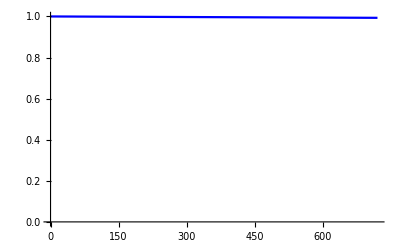

```mathematica
plot1m=ListLinePlot[prob1movr2y, PlotStyle->Blue, PlotRange->{0,1}]
```

```mathematica
probnoreinf3mtimecourse=Take[sarscov2probnoreinfectiontimecourse,90];
probnoreinf3m=Part[sarscov2probnoreinfectiontimecourse, 90];
prob3movr6y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,23]];
prob3movr2y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,7]];
```

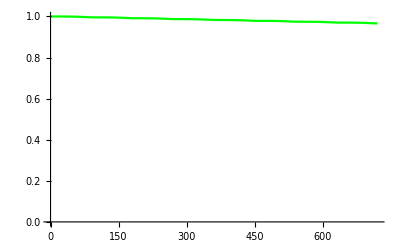

```mathematica
plot3m=ListLinePlot[prob3movr2y, PlotStyle->Green, PlotRange->{0,1}]
```

```mathematica
probnoreinf6mtimecourse=Take[sarscov2probnoreinfectiontimecourse,183];
probnoreinf6m=Part[sarscov2probnoreinfectiontimecourse, 183];
prob6movr6y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,11]];
prob6movr2y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,3]];
```

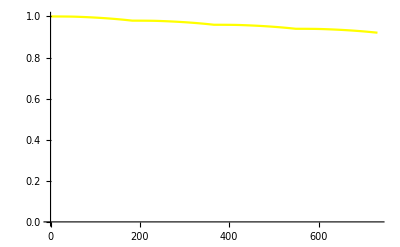

```mathematica
plot6m=ListLinePlot[prob6movr2y, PlotStyle->Yellow, PlotRange->{0,1}]
```

```mathematica
probnoreinf1ytimecourse=Take[sarscov2probnoreinfectiontimecourse,365];
probnoreinf1y=Part[sarscov2probnoreinfectiontimecourse, 365];
prob1yovr6y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,5]];
prob1yovr2y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,1]];
```

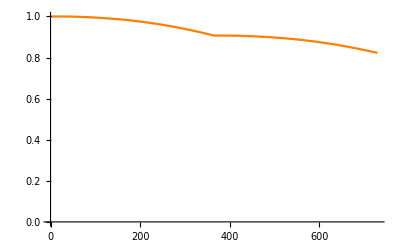

```mathematica
plot1y=ListLinePlot[prob1yovr2y, PlotStyle->Orange, PlotRange->{0,1}]
```

```mathematica
probnoreinf2ytimecourse=Take[sarscov2probnoreinfectiontimecourse,730];
probnoreinf2y=Part[sarscov2probnoreinfectiontimecourse, 730];
prob2yovr6y=Catenate[NestList[#*probnoreinf2y&,probnoreinf2ytimecourse,2]];
prob2yovr2y=Take[sarscov2probnoreinfectiontimecourse,730];
```

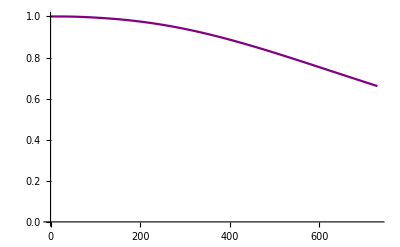

```mathematica
plot2y=ListLinePlot[prob2yovr2y, PlotStyle->Purple, PlotRange->{0,1}]
```

```mathematica
probnoreinf6ytimecourse=Take[sarscov2probnoreinfectiontimecourse,2190];
```

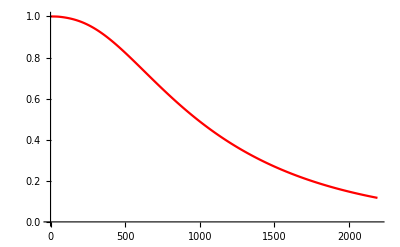

```mathematica
plot6y=ListLinePlot[probnoreinf6ytimecourse, PlotStyle->Red, PlotRange->{0,1}]
```

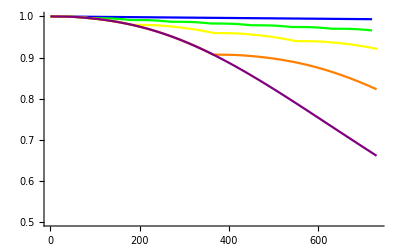

```mathematica
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1}]
```

```mathematica
Export[
StringJoin["/Users/hayley/Documents/townsend/spring-23/cancer/figs/chemo_boosterovrtime-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

/Users/hayley/Documents/townsend/spring-23/cancer/figs/chemo_boosterovrtime-by-Day_04May2023.pdf

```mathematica
Show[1-Last[prob2yovr2y], 1-Last[prob1yovr2y], 1-Last[prob6movr2y], 1-Last[prob3movr2y],1-Last[prob1movr2y]]
```

Show::gcomb: Could not combine the graphics objects in Show[0.338996,0.177303,0.0791729,0.0339851,0.00669202].

Show[0.338996,0.177303,0.0791729,0.0339851,0.00669202]

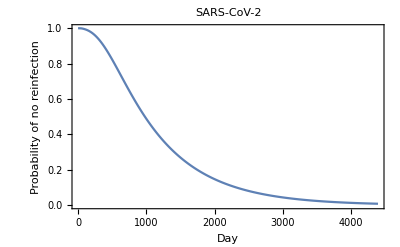

```mathematica
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability of no reinfection"}]
```

```mathematica
Export[
StringJoin["/Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_04May2023.pdf.

$Failed

```mathematica
sarscov2continuousprobnoreinfection=Interpolation[sarscov2probnoreinfectiontimecourse]
```

InterpolatingFunction[…]

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.95],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{274.686,9.15621,0.752565}

These are the 5% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.50],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{980.352,32.6784,2.6859}

These are the 50% quantiles (medians) for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.05],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{2891.35,96.3785,7.92152}

These are the 95% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
sarscov2probreinfectiondensity={};
day=0;
While[day<4393,
Increment[day];
AppendTo[sarscov2probreinfectiondensity, 
If[day<1201,
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day]]]*sarscov2probnoreinfectiontimecourse[[day]],
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]]*sarscov2probnoreinfectiontimecourse[[day]]
]
]
];
```

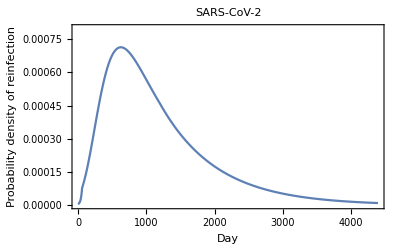

```mathematica
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0008},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0005},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_04May2023.pdf.

$Failed